# Exact

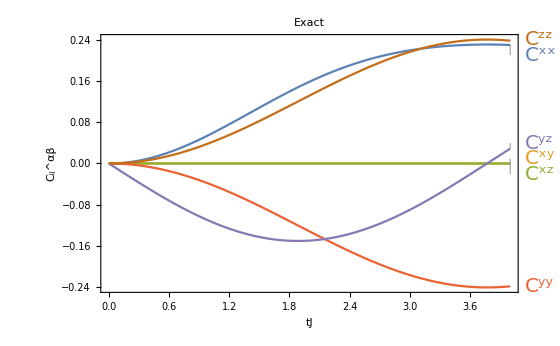

```mathematica
ClearAll["Global`*"]
jstrength=1;(*Interaction Strength (default is 1)*)
θ=π/2;(*Polar Angle*)
ϕ=0;
alpha =3;
num=2;

j=1;
h= 1/3;
list=Table[{4,i,0},{i,num}];
site1 = list[[1]];
site2 = list[[2]];
tmax=4;




pauli=(1/2)Table[PauliMatrix[i],{i,3}];
SparseIdentityMatrix[n_ ]:=SparseArray[Band[{1,1}]->1, {n,n}];

(*k is site, l is signifying x y or z*)
op[k_,a_?MatrixQ]:= KroneckerProduct[SparseIdentityMatrix[(2)^(k-1)],a,SparseIdentityMatrix[(2)^(num-k)]];
xyz[k_,l_]:=op[k,pauli[[l]]];
(*transverse ising hamiltonian*)
H[h_]:= -(h)*Sum[xyz[k,1],{k,num}]-(j)*Sum[xyz[k,3].xyz[k+1,3],{k,num-1}];
(*productstate[state_?VectorQ]:= Flatten[KroneckerProduct@@Table[state, {n}]];*)

productstate[array_]:= Flatten[KroneckerProduct@@array];
basis[a_]:=SparseArray[a->1,2];
up=SparseArray[1->1,2];
down=SparseArray[-1->1,2];
single=Cos[θ/2]up + ⅇ^(I ϕ)Sin[θ/2]down;


psi[t_] :=Table[q[i][t],{i,1,2^num}];

variables =Array[q,2^num];
ndsolve =Flatten[NDSolve[{I Normal[psi'[t]]==H[h].Normal[psi[t]],Normal[psi[0]]==Normal[productstate[Table[single,num]]]},variables,{t,0,tmax}]];

result[t_]:=Normal[psi[t]]/.ndsolve ;

EV[operator_,t_]:=Re[result[t]*.(operator.result[t])];
(*to calculate expectation values: <psi|operator|psi>*)
b[site_,t_]:=Table[EV[xyz[site[[2]],a],t],{a,{1,2,3}}];

(*correlation values*)
connected[t_]:=Table[EV[(xyz[site1[[2]],a].xyz[site2[[2]],b]),t]-EV[xyz[site1[[2]],a],t]EV[xyz[site2[[2]],b],t],{a,{1,2,3}},{b,{1,2,3}}];

Plot[Evaluate[Delete[Flatten[connected[time]],{{4},{7},{8}}]],{time,0,4},PlotRange->All,PlotLabel->"Exact",PlotLabels->{Style[Superscript["C","xx"],"TimesNewRoman",Italic,ColorData[97,1]],Style[Superscript["C","xy"],"TimesNewRoman",Italic,ColorData[97,2]],Style[Superscript["C","xz"],"TimesNewRoman",Italic,ColorData[97,3]],Style[Superscript["C","yy"],"TimesNewRoman",Italic,ColorData[97,4]],Style[Superscript["C","yz"],"TimesNewRoman",Italic,ColorData[97,5]],Style[Superscript["C","zz"],"TimesNewRoman",Italic,ColorData[97,6]]},ImageSize->560,FrameLabel->{Style["tJ",Italic,28],Style[Subsuperscript["C","ij","αβ"],28]},Frame->True,RotateLabel->False,LabelStyle->Directive[FontSize->20,Black,FontFamily->"Times New Roman"]]
```

# DTWA

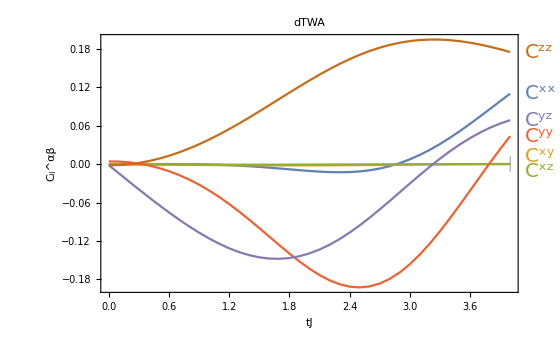

```mathematica
ClearAll["Global`*"]
jstrength=1;(*Interaction Strength (default is 1)*)
θ=π/2;(*Polar Angle*)

tmax=4;
samples = 10000;
num =2;
site1 = 1;
site2 = 2;
h = 1/3;

(*Define Interactions & Bloch Vector*)(*everything in terms of S, not sigma*)
(*1 is x, -1 is y, 0 is z*)
(*add d, etc. for additional spins*)
cutoff[epsilon_]:=If[Abs[epsilon] > 10^-8,epsilon,0];

J[i_,j_]:=(m= Abs[i-j];If[m==1,1,0])(*If[EuclideanDistance[i,j]==1,jstrength,0]*)(*1/Abs[j-i]^3*); (*Interaction function J depends on experimental scenario, these are two examples*)

ident = {{1,0},{0,1}};
pauli=Table[PauliMatrix[i],{i,3}];
phasepoints = {{1,1,1},{-1,-1,1},{1,-1,-1},{-1,1,-1}};
operator[r_]:=(ident+r.pauli)/2;
wigner[i_]:=Tr[operator[{Sin[θ],0,Cos[θ]}].operator[phasepoints[[i]]]]/2;
phasespace = Table[wigner[i],{i,4}];

Px = phasespace[[1]]+phasespace[[3]];
Py = phasespace[[1]]+phasespace[[4]];
Pz = phasespace[[1]]+phasespace[[2]];

biglist=Table[(1/2){RandomChoice[{Px,1-Px}->{1,-1}],RandomChoice[{Py,1-Py}->{1,-1}],RandomChoice[{Pz,1-Pz}->{1,-1}]},{a,1,samples},{b,1,num}];
beta[component_]:= Sum[J[spin,other]*Switch[component,1,x[other][time],2,y[other][time],3,z[other][time]],{other,1,num}];

value2[j_,k_]:=Sum[
(
samplelist=biglist[[sample]];
evolve = Table[
(initial=Flatten[Table[{x[i][0]==samplelist[[i]][[1]],y[i][0]==samplelist[[i]][[2]],z[i][0]==samplelist[[i]][[3]]},{i,num}]];
difeq=Flatten[Table[{x[i]'[time]==y[i][time]*beta[3],y[i]'[time]==-x[i][time]*beta[3]+h z[i][time],z[i]'[time]==-h y[i][time]},{i,num}]];
NDSolveValue[Join[difeq, initial],{x[spin][t],y[spin][t],z[spin][t]},{time,0,tmax}]
),{spin,{j,k}}];
Table[evolve[[1]][[a]]*evolve[[2]][[b]], {a,{1,2,3}},{b,{1,2,3}}]
)
,{sample,1,samples}]/samples

value1[j_]:=Sum[
(
samplelist=biglist[[sample]];
evolve = Table[
(initial=Flatten[Table[{x[i][0]==samplelist[[i]][[1]],y[i][0]==samplelist[[i]][[2]],z[i][0]==samplelist[[i]][[3]]},{i,num}]];
difeq=Flatten[Table[{x[i]'[time]==y[i][time]*beta[3],y[i]'[time]==-x[i][time]*beta[3]+h z[i][time],z[i]'[time]==-h y[i][time]},{i,num}]];
NDSolveValue[Join[difeq, initial],{x[spin][t],y[spin][t],z[spin][t]},{time,0,tmax}]
),{spin,{j}}];
Table[evolve[[1]][[a]],{a,{1,2,3}}]
)
,{sample,1,samples}]/samples

corr2 = N[value2[site1,site2]];
corr1j=N[value1[site1]];
corr1k=N[value1[site2]];

connected=Table[corr2[[a]][[b]]-corr1j[[a]]corr1k[[b]],{a,{1,2,3}},{b,{1,2,3}}];

ListPlot[Table[(t=time;{time,Flatten[connected][[k]]}),{k,{1,2,3,5,6,9}},{time,0,4,0.1}],PlotRange->All,PlotLabel->"dTWA",PlotLabels->{Style[Superscript["C","xx"],"TimesNewRoman",Italic,ColorData[97,1]],Style[Superscript["C","xy"],"TimesNewRoman",Italic,ColorData[97,2]],Style[Superscript["C","xz"],"TimesNewRoman",Italic,ColorData[97,3]],Style[Superscript["C","yy"],"TimesNewRoman",Italic,ColorData[97,4]],Style[Superscript["C","yz"],"TimesNewRoman",Italic,ColorData[97,5]],Style[Superscript["C","zz"],"TimesNewRoman",Italic,ColorData[97,6]]},ImageSize->560,FrameLabel->{Style["tJ",Italic,28],Style[Subsuperscript["C","ij","αβ"],28]},Frame->True,RotateLabel->False,LabelStyle->Directive[FontSize->20,Black,FontFamily->"Times New Roman"],Joined->True]
```

# TWA

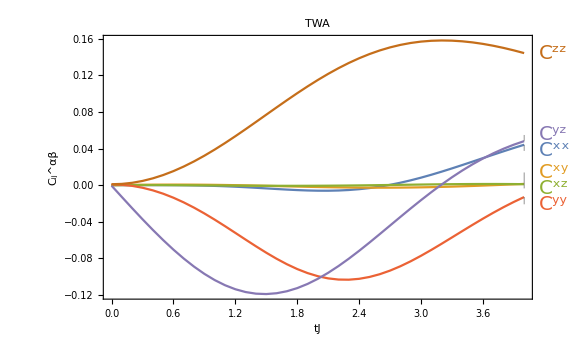

```mathematica
(*how to generalize:change polynomial by adding another xyz vector and changing the exponent in the scale factor, change  functions to accept four variables instead of three, input correct cumulant definition into connected, create Formula4[] and Four[] based on previous formulas which is easy extension, possibly change the contour value given to plot[] depending on the order of magnitude of the new correlations*)
ClearAll["Global`*"]
jstrength=1;(*Interaction Strength (default is 1)*)
θ=π/2;(*Polar Angle*)

samples = 20000;
num =2;
site1 = 1;
site2 = 2;
h=1/3;
tmax=4;

S = num/2;
Sz = S; (*removed the Dirac delta*)
beta[component_]:= Sum[J[spin,other]*Switch[component,1,x[other][time],2,y[other][time],3,z[other][time]],{other,1,num}];
individual=ProbabilityDistribution[(π*S)^(-1/2)ⅇ^(-(Spin^2)/S),{Spin,-Infinity,Infinity}];
wignershift = RotationMatrix[θ, {0,1,0}];
cdf = CDF[individual,root];
data=Table[If[condition==3,Sz/num,(root/.FindRoot[RandomReal[]==cdf,{root,1}])/Sqrt[num]],{samples},{num},{condition,3}];
cutoff[epsilon_]:=If[Abs[epsilon] > 10^-8,epsilon,0];
J[i_,j_]:=If[Abs[i-j]==1,jstrength,0];

value2[j_,k_]:=Sum[
(random = data[[sample]];
rotrandom = Table[wignershift.random[[w]],{w,num}];

evolve = Table[
(initial=Flatten[Table[{x[i][0]==rotrandom[[i]][[1]],y[i][0]==rotrandom[[i]][[2]],z[i][0]==rotrandom[[i]][[3]]},{i,num}]];
difeq=Flatten[Table[{x[i]'[time]==y[i][time]*beta[3],y[i]'[time]==-x[i][time]*beta[3]+h z[i][time],z[i]'[time]==-h y[i][time]},{i,num}]];
NDSolveValue[Join[difeq, initial],{x[spin][t],y[spin][t],z[spin][t]},{time,0,tmax}]
),{spin,{j,k}}];
Table[evolve[[1]][[a]]*evolve[[2]][[b]], {a,{1,2,3}},{b,{1,2,3}}]
)
,{sample,1,samples}]/samples;

value1[j_]:=Sum[
(random = data[[sample]];
rotrandom = Table[wignershift.random[[w]],{w,num}];

evolve = Table[
(initial=Flatten[Table[{x[i][0]==rotrandom[[i]][[1]],y[i][0]==rotrandom[[i]][[2]],z[i][0]==rotrandom[[i]][[3]]},{i,num}]];
difeq=Flatten[Table[{x[i]'[time]==y[i][time]*beta[3],y[i]'[time]==-x[i][time]*beta[3]+h z[i][time],z[i]'[time]==-h y[i][time]},{i,num}]];
NDSolveValue[Join[difeq, initial],{x[spin][t],y[spin][t],z[spin][t]},{time,0,tmax}]
),{spin,{j}}];
Table[evolve[[1]][[a]],{a,{1,2,3}}]
)
,{sample,1,samples}]/samples;

corr2 = N[value2[site1,site2]];
corr1j=N[value1[site1]];
corr1k=N[value1[site2]];

connected=Table[corr2[[a]][[b]]-corr1j[[a]]corr1k[[b]],{a,{1,2,3}},{b,{1,2,3}}];

(*ListPlot[Table[{time,(t=time;value2[10,11]-value1[10][[2]]value1[11][[3]])},{time,0,12,0.1}],PlotRange->All,PlotStyle->{Red}]*)
ListPlot[Table[(t=timepoint;{timepoint,Flatten[connected][[k]]}),{k,{1,2,3,5,6,9}},{timepoint,0,4,0.1}],PlotRange->All,PlotLabel->"TWA",PlotLabels->{Style[Superscript["C","xx"],"TimesNewRoman",Italic,ColorData[97,1]],Style[Superscript["C","xy"],"TimesNewRoman",Italic,ColorData[97,2]],Style[Superscript["C","xz"],"TimesNewRoman",Italic,ColorData[97,3]],Style[Superscript["C","yy"],"TimesNewRoman",Italic,ColorData[97,4]],Style[Superscript["C","yz"],"TimesNewRoman",Italic,ColorData[97,5]],Style[Superscript["C","zz"],"TimesNewRoman",Italic,ColorData[97,6]]},ImageSize->560,FrameLabel->{Style["tJ",Italic,28],Style[Subsuperscript["C","ij","αβ"],28]},Frame->True,RotateLabel->False,LabelStyle->Directive[FontSize->20,Black,FontFamily->"Times New Roman"],Joined->True]
```